```mathematica
n = 100;
Ys = Table[0,{n+1}];
h = 1./n;
h
```

0.01

```mathematica
Xs = Table[i*h,{i,0,n}];
```

```mathematica
Xs
```

{0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
Ys[[1]] = 0.01;
```

```mathematica
For[i = 2, i≤n,i++, Ys[[i]] = Ys[[i-1]] + h* (10*Ys[[i-1]]*(1-Ys[[i-1]]))]
```

```mathematica
Ys
```

{0.01,0.01099,0.0120769,0.01327,0.0145794,0.0160161,0.0175921,0.0193203,0.021215,0.0232915,0.0255664,0.0280577,0.0307848,0.0337685,0.0370313,0.0405973,0.0444922,0.0487435,0.0533802,0.0584333,0.0639352,0.0699199,0.076423,0.0834813,0.0911325,0.0994152,0.108368,0.118031,0.128441,0.139635,0.151649,0.164514,0.178259,0.192907,0.208477,0.224978,0.242414,0.260779,0.280057,0.300219,0.321228,0.343032,0.365568,0.388761,0.412524,0.436758,0.461358,0.486209,0.51119,0.536178,0.561047,0.585674,0.60994,0.633731,0.656943,0.67948,0.701258,0.722208,0.74227,0.761401,0.779568,0.796752,0.812946,0.828152,0.842384,0.855661,0.868012,0.879468,0.890069,0.899853,0.908865,0.917148,0.924747,0.931706,0.938069,0.943878,0.949176,0.954,0.958388,0.962376,0.965997,0.969282,0.972259,0.974956,0.977398,0.979607,0.981605,0.98341,0.985042,0.986515,0.987846,0.989046,0.99013,0.991107,0.991988,0.992783,0.9935,0.994145,0.994727,0.995252,0}

Part::partd: Part specification Ys ⟦ 1 ⟧ is longer than depth of object.

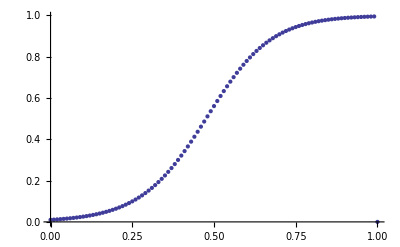

```mathematica
p1 = ListPlot[Transpose[{Xs,Ys}]]
```

```mathematica
Ys2= Table[0,{n+1}]; Ys2[[1]]=0.01;
```

```mathematica
For[i = 2, i≤n,i++,Ys2[[i]] = temp /. FindRoot[temp== Ys2[[i-1]] + h*10*temp*(1-temp), {temp,0}]]
```

```mathematica
$Aborted Ys
```

```mathematica
Ys2
```

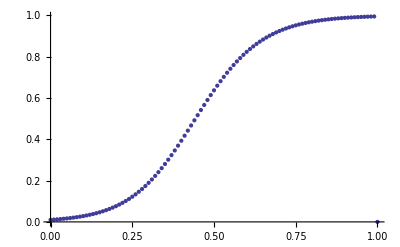

```mathematica
p2 = ListPlot[Transpose[{Xs,Ys2}]]
```

```mathematica
Show[p1,p2]
```